## Waveform of the Quasi-circular System

```mathematica
Remove["Global`*"]
```

Remove::rmnsm: There are no symbols matching "Global`*".

### Plus and Cross Polarization Tensors

First, we will determine an orthonormal set of unit vectors in the rotated frame. An immediate choice would be rotating the  unit vector by an angle of  about the -axis.

```mathematica
u={{Cos[-ϕ],-Sin[-ϕ],0}, {Sin[-ϕ],Cos[-ϕ],0},{0,0,1}}.{{1,0,0}, {0,Cos[-ι],-Sin[-ι]}, {0,Sin[-ι],Cos[-ι]}}.{{1},{0},{0}};
 v={{Cos[-ϕ],-Sin[-ϕ],0}, {Sin[-ϕ],Cos[-ϕ],0},{0,0,1}}.{{1,0,0}, {0,Cos[-ι],-Sin[-ι]}, {0,Sin[-ι],Cos[-ι]}}  .{{0},{1},{0}};
 n={{Cos[-ϕ],-Sin[-ϕ],0}, {Sin[-ϕ],Cos[-ϕ],0},{0,0,1}}.{{1,0,0},{0,Cos[-ι],-Sin[-ι]},{0,Sin[-ι],Cos[-ι]}} .{{0},{0},{1}};
```

The traceless tensors  and  that are transverse to the unit vector pointing to the observer are as follows.

```mathematica
Subscript[A, plus]=u.Transpose[u]-v.Transpose[v];
Subscript[A, plus]//MatrixForm//Simplify
```

(Cos[ϕ]^2-Cos[ι]^2 Sin[ϕ]^2 | -((1+Cos[ι]^2) Cos[ϕ] Sin[ϕ]) | Cos[ι] Sin[ι] Sin[ϕ]
-((1+Cos[ι]^2) Cos[ϕ] Sin[ϕ]) | -Cos[ι]^2 Cos[ϕ]^2+Sin[ϕ]^2 | Cos[ι] Cos[ϕ] Sin[ι]
Cos[ι] Sin[ι] Sin[ϕ] | Cos[ι] Cos[ϕ] Sin[ι] | -Sin[ι]^2)

```mathematica
Subscript[A, cross]=u.Transpose[v]+v.Transpose[u];
Subscript[A, cross]//MatrixForm//Simplify
```

(Cos[ι] Sin[2 ϕ] | Cos[ι] Cos[2 ϕ] | -Cos[ϕ] Sin[ι]
Cos[ι] Cos[2 ϕ] | -2 Cos[ι] Cos[ϕ] Sin[ϕ] | Sin[ι] Sin[ϕ]
-Cos[ϕ] Sin[ι] | Sin[ι] Sin[ϕ] | 0)

When contracted together, we have the following.

```mathematica
Tr[Subscript[A, plus].Transpose[Subscript[A, cross]]]//Simplify
```

0

```mathematica
Tr[Subscript[A, plus].Transpose[Subscript[A, plus]]]//Simplify
```

2

From this, we have the following:

```mathematica
Tr[Transpose[{{Subscript[M, 11],Subscript[M, 12],0},{Subscript[M, 12],Subscript[M, 22],0},{0,0,0}}].Subscript[A, plus]]//FullSimplify
```

(Cos[ϕ]^2-Cos[ι]^2 Sin[ϕ]^2) M_11-1/2 (3+Cos[2 ι]) Sin[2 ϕ] M_12+(-Cos[ι]^2 Cos[ϕ]^2+Sin[ϕ]^2) M_22

```mathematica
(1+Cos[ι]^2) TrigReduce[Cos[ϕ]^2 Subscript[M, 11]-Sin[ϕ]^2 Subscript[M, 11]-2 Cos[ϕ] Sin[ϕ] Subscript[M, 12]]
```

(1+Cos[ι]^2) (Cos[2 ϕ] M_11-Sin[2 ϕ] M_12)

```mathematica
Tr[Transpose[{{Subscript[M, 11],Subscript[M, 12],0},{Subscript[M, 12],Subscript[M, 22],0},{0,0,0}}].Subscript[A, cross]]//Factor
```

2 Cos[ι] (Cos[ϕ] Sin[ϕ] M_11+Cos[ϕ]^2 M_12-Sin[ϕ]^2 M_12-Cos[ϕ] Sin[ϕ] M_22)

```mathematica
2 Cos[ι] TrigReduce[2 Cos[ϕ] Sin[ϕ] Subscript[M, 11]+Cos[ϕ]^2 Subscript[M, 12]-Sin[ϕ]^2 Subscript[M, 12]]
```

2 Cos[ι] (Sin[2 ϕ] M_11+Cos[2 ϕ] M_12)

### Binary System

#### Mass Quadrupole Radiation

Using the energy balance equation, the frequency evolution is

```mathematica
DSolve[ω'[t]==96/5 ℳ^(5/3)ω[t]^(11/3),ω[t],t]//Simplify
```

{{ω[t]→1/(2 2^(1/8) (-32/5 t ℳ^(5/3)-C[1]/3)^(3/8))}}

```mathematica
Integrate[-5^(3/8)/8 ℳ^(-5/8)(t-c)^(-3/8),t]//FullSimplify
```

-(-c+t)^(5/8)/(5^(5/8) ℳ^(5/8))

```mathematica
5^(5/8)
```

5^(5/8)

### Lagrange Three-body System

#### Configuration of the Lagrange Three-body System

Let

```mathematica
Subscript[R, 1]=b/(√3)(E^(2π I/3)-(1-Subscript[β, 2]-Subscript[β, 3])E^(2π I/3)-Subscript[β, 2] E^(-2π I/3)-Subscript[β, 3])//ComplexExpand//Factor
```

-1/2 b (-2 ⅈ β_2-ⅈ β_3+√3 β_3)

```mathematica
Subscript[R, 2]=b/(√3)(E^(-2π I/3)-Subscript[β, 1] E^(2π I/3)-(1-Subscript[β, 1]-Subscript[β, 3])E^(-2π I/3)-Subscript[β, 3])//ComplexExpand//Factor
```

-1/2 b (2 ⅈ β_1+ⅈ β_3+√3 β_3)

```mathematica
Subscript[R, 3]=b/(√3)(1-Subscript[β, 1] E^(2π I/3)-Subscript[β, 2] E^(-2π I/3)-(1-Subscript[β, 1]-Subscript[β, 2]))//ComplexExpand//Factor
```

1/2 b (-ⅈ β_1+√3 β_1+ⅈ β_2+√3 β_2)

```mathematica
Subscript[X, 1]=FullSimplify[ComplexExpand[Abs[Subscript[R, 1]]],Assumptions->b>0]
Subscript[X, 2]=FullSimplify[ComplexExpand[Abs[Subscript[R, 2]]],Assumptions->b>0]
Subscript[X, 3]=FullSimplify[ComplexExpand[Abs[Subscript[R, 3]]],Assumptions->b>0]
```

b √(β_2^2+β_2 β_3+β_3^2)

b √(β_1^2+β_1 β_3+β_3^2)

b √(β_1^2+β_1 β_2+β_2^2)

```mathematica
(Subscript[R, 1]//ComplexExpand)/Subscript[X, 1]
(Subscript[R, 2]//ComplexExpand)/Subscript[X, 2]
(Subscript[R, 3]//ComplexExpand)/Subscript[X, 3]
```

(-1/2 √3 b β_3+ⅈ (b β_2+(b β_3)/2))/(b √(β_2^2+β_2 β_3+β_3^2))

(-1/2 √3 b β_3+ⅈ (-b β_1-(b β_3)/2))/(b √(β_1^2+β_1 β_3+β_3^2))

(1/2 √3 b β_1+1/2 √3 b β_2+ⅈ (-(b β_1)/2+(b β_2)/2))/(b √(β_1^2+β_1 β_2+β_2^2))

```mathematica
SingleAngle:={Cos[Subscript[θ, 1]]->FullSimplify[ComplexExpand[Re[Subscript[R, 1]/Subscript[X, 1]]],Assumptions->{Subscript[β, 1]∈Reals,Subscript[β, 2]∈Reals,Subscript[β, 3]∈Reals}],
Sin[Subscript[θ, 1]]->FullSimplify[ComplexExpand[Im[Subscript[R, 1]/Subscript[X, 1]]],Assumptions->{Subscript[β, 1]∈Reals,Subscript[β, 2]∈Reals,Subscript[β, 3]∈Reals}],Cos[Subscript[θ, 2]]->FullSimplify[ComplexExpand[Re[Subscript[R, 2]/Subscript[X, 2]]],Assumptions->{Subscript[β, 1]∈Reals,Subscript[β, 2]∈Reals,Subscript[β, 3]∈Reals}],Sin[Subscript[θ, 2]]->FullSimplify[ComplexExpand[Im[Subscript[R, 2]/Subscript[X, 2]]],Assumptions->{Subscript[β, 1]∈Reals,Subscript[β, 2]∈Reals,Subscript[β, 3]∈Reals}],Cos[Subscript[θ, 3]]->FullSimplify[ComplexExpand[Re[Subscript[R, 3]/Subscript[X, 3]]],Assumptions->{Subscript[β, 1]∈Reals,Subscript[β, 2]∈Reals,Subscript[β, 3]∈Reals}],Sin[Subscript[θ, 3]]->FullSimplify[ComplexExpand[Im[Subscript[R, 3]/Subscript[X, 3]]],Assumptions->{Subscript[β, 1]∈Reals,Subscript[β, 2]∈Reals,Subscript[β, 3]∈Reals}],Subscript[m, 1]->Subscript[β, 1] M,Subscript[m, 2]->Subscript[β, 2] M,Subscript[m, 3]->Subscript[β, 3] M};
```

```mathematica
SingleAngle
```

{Cos[θ_1]→-(√3 β_3)/(2 √(β_2^2+β_2 β_3+β_3^2)),Sin[θ_1]→(2 β_2+β_3)/(2 √(β_2^2+β_2 β_3+β_3^2)),Cos[θ_2]→-(√3 β_3)/(2 √(β_1^2+β_1 β_3+β_3^2)),Sin[θ_2]→-(2 β_1+β_3)/(2 √(β_1^2+β_1 β_3+β_3^2)),Cos[θ_3]→(√3 (β_1+β_2))/(2 √(β_1^2+β_1 β_2+β_2^2)),Sin[θ_3]→(-β_1+β_2)/(2 √(β_1^2+β_1 β_2+β_2^2)),m_1→M β_1,m_2→M β_2,m_3→M β_3}

The double-angle identities are as follows:

```mathematica
(Subscript[R, 1]^2//ComplexExpand)/Subscript[X, 1]^2
(Subscript[R, 2]^2//ComplexExpand)/Subscript[X, 2]^2
(Subscript[R, 3]^2//ComplexExpand)/Subscript[X, 3]^2
```

(-b^2 β_2^2-b^2 β_2 β_3+1/2 b^2 β_3^2+ⅈ (-√3 b^2 β_2 β_3-1/2 √3 b^2 β_3^2))/(b^2 (β_2^2+β_2 β_3+β_3^2))

(-b^2 β_1^2-b^2 β_1 β_3+1/2 b^2 β_3^2+ⅈ (√3 b^2 β_1 β_3+1/2 √3 b^2 β_3^2))/(b^2 (β_1^2+β_1 β_3+β_3^2))

(1/2 b^2 β_1^2+2 b^2 β_1 β_2+1/2 b^2 β_2^2+ⅈ (-1/2 √3 b^2 β_1^2+1/2 √3 b^2 β_2^2))/(b^2 (β_1^2+β_1 β_2+β_2^2))

```mathematica
DoubleAngle:={Cos[2 Subscript[θ, 1]]->ComplexExpand[Re[Subscript[R, 1]^2/Subscript[X, 1]^2]],
Sin[2 Subscript[θ, 1]]->ComplexExpand[Im[Subscript[R, 1]^2/Subscript[X, 1]^2]],Cos[2 Subscript[θ, 2]]->ComplexExpand[Re[Subscript[R, 2]^2/Subscript[X, 2]^2]],Sin[2 Subscript[θ, 2]]->ComplexExpand[Im[Subscript[R, 2]^2/Subscript[X, 2]^2]],Cos[2 Subscript[θ, 3]]->ComplexExpand[Re[Subscript[R, 3]^2/Subscript[X, 3]^2]],Sin[2 Subscript[θ, 3]]->ComplexExpand[Im[Subscript[R, 3]^2/Subscript[X, 3]^2]],Subscript[m, 1]->Subscript[β, 1] M,Subscript[m, 2]->Subscript[β, 2] M,Subscript[m, 3]->Subscript[β, 3] M};
```

```mathematica
DoubleAngle
```

{Cos[2 θ_1]→-β_2^2/(β_2^2+β_2 β_3+β_3^2)-(β_2 β_3)/(β_2^2+β_2 β_3+β_3^2)+β_3^2/(2 (β_2^2+β_2 β_3+β_3^2)),Sin[2 θ_1]→-(√3 β_2 β_3)/(β_2^2+β_2 β_3+β_3^2)-(√3 β_3^2)/(2 (β_2^2+β_2 β_3+β_3^2)),Cos[2 θ_2]→-β_1^2/(β_1^2+β_1 β_3+β_3^2)-(β_1 β_3)/(β_1^2+β_1 β_3+β_3^2)+β_3^2/(2 (β_1^2+β_1 β_3+β_3^2)),Sin[2 θ_2]→(√3 β_1 β_3)/(β_1^2+β_1 β_3+β_3^2)+(√3 β_3^2)/(2 (β_1^2+β_1 β_3+β_3^2)),Cos[2 θ_3]→β_1^2/(2 (β_1^2+β_1 β_2+β_2^2))+(2 β_1 β_2)/(β_1^2+β_1 β_2+β_2^2)+β_2^2/(2 (β_1^2+β_1 β_2+β_2^2)),Sin[2 θ_3]→-(√3 β_1^2)/(2 (β_1^2+β_1 β_2+β_2^2))+(√3 β_2^2)/(2 (β_1^2+β_1 β_2+β_2^2)),m_1→M β_1,m_2→M β_2,m_3→M β_3}

The triple-angle identities are as follows:

```mathematica
(Subscript[R, 1]^3//ComplexExpand)/Subscript[X, 1]^3
(Subscript[R, 2]^3//ComplexExpand)/Subscript[X, 2]^3
(Subscript[R, 3]^3//ComplexExpand)/Subscript[X, 3]^3
```

(3/2 √3 b^3 β_2^2 β_3+3/2 √3 b^3 β_2 β_3^2+ⅈ (-b^3 β_2^3-3/2 b^3 β_2^2 β_3+3/2 b^3 β_2 β_3^2+b^3 β_3^3))/(b^3 (β_2^2+β_2 β_3+β_3^2)^(3/2))

(3/2 √3 b^3 β_1^2 β_3+3/2 √3 b^3 β_1 β_3^2+ⅈ (b^3 β_1^3+3/2 b^3 β_1^2 β_3-3/2 b^3 β_1 β_3^2-b^3 β_3^3))/(b^3 (β_1^2+β_1 β_3+β_3^2)^(3/2))

(3/2 √3 b^3 β_1^2 β_2+3/2 √3 b^3 β_1 β_2^2+ⅈ (-b^3 β_1^3-3/2 b^3 β_1^2 β_2+3/2 b^3 β_1 β_2^2+b^3 β_2^3))/(b^3 (β_1^2+β_1 β_2+β_2^2)^(3/2))

```mathematica
TripleAngle:={Cos[3 Subscript[θ, 1]]->FullSimplify[ComplexExpand[Re[Subscript[R, 1]^3/Subscript[X, 1]^3]],Assumptions->{Subscript[β, 1]∈Reals,Subscript[β, 2]∈Reals,Subscript[β, 3]∈Reals}],
Sin[3 Subscript[θ, 1]]->FullSimplify[ComplexExpand[Im[Subscript[R, 1]^3/Subscript[X, 1]^3]],Assumptions->{Subscript[β, 1]∈Reals,Subscript[β, 2]∈Reals,Subscript[β, 3]∈Reals}],Cos[3 Subscript[θ, 2]]->FullSimplify[ComplexExpand[Re[Subscript[R, 2]^3/Subscript[X, 2]^3]],Assumptions->{Subscript[β, 1]∈Reals,Subscript[β, 2]∈Reals,Subscript[β, 3]∈Reals}],Sin[3 Subscript[θ, 2]]->FullSimplify[ComplexExpand[Im[Subscript[R, 2]^3/Subscript[X, 2]^3]],Assumptions->{Subscript[β, 1]∈Reals,Subscript[β, 2]∈Reals,Subscript[β, 3]∈Reals}],Cos[3 Subscript[θ, 3]]->FullSimplify[ComplexExpand[Re[Subscript[R, 3]^3/Subscript[X, 3]^3]],Assumptions->{Subscript[β, 1]∈Reals,Subscript[β, 2]∈Reals,Subscript[β, 3]∈Reals}],Sin[3 Subscript[θ, 3]]->FullSimplify[ComplexExpand[Im[Subscript[R, 3]^3/Subscript[X, 3]^3]],Assumptions->{Subscript[β, 1]∈Reals,Subscript[β, 2]∈Reals,Subscript[β, 3]∈Reals}],Subscript[m, 1]->Subscript[β, 1] M,Subscript[m, 2]->Subscript[β, 2] M,Subscript[m, 3]->Subscript[β, 3] M};
```

```mathematica
TripleAngle
```

{Cos[3 θ_1]→(3 √3 β_2 β_3 (β_2+β_3))/(2 (β_2^2+β_2 β_3+β_3^2)^(3/2)),Sin[3 θ_1]→-((β_2-β_3) (2 β_2+β_3) (β_2+2 β_3))/(2 (β_2^2+β_2 β_3+β_3^2)^(3/2)),Cos[3 θ_2]→(3 √3 β_1 β_3 (β_1+β_3))/(2 (β_1^2+β_1 β_3+β_3^2)^(3/2)),Sin[3 θ_2]→((β_1-β_3) (2 β_1+β_3) (β_1+2 β_3))/(2 (β_1^2+β_1 β_3+β_3^2)^(3/2)),Cos[3 θ_3]→(3 √3 β_1 β_2 (β_1+β_2))/(2 (β_1^2+β_1 β_2+β_2^2)^(3/2)),Sin[3 θ_3]→-((β_1-β_2) (2 β_1+β_2) (β_1+2 β_2))/(2 (β_1^2+β_1 β_2+β_2^2)^(3/2)),m_1→M β_1,m_2→M β_2,m_3→M β_3}

```mathematica
(Subscript[β, 3](Subscript[β, 1]+Subscript[β, 2])-2 Subscript[β, 1] Subscript[β, 2])^2+3 Subscript[β, 3]^2(Subscript[β, 1]-Subscript[β, 2])^2//Expand//Factor
```

4 (β_1^2 β_2^2-β_1^2 β_2 β_3-β_1 β_2^2 β_3+β_1^2 β_3^2-β_1 β_2 β_3^2+β_2^2 β_3^2)

#### Mass Quadrupole Radiation

The plus polarization of the mass quadrupole radiation is

```mathematica
(1+Cos[ι]^2) (-Cos[2 ϕ] ( ∑_(p=1)^3 (2 ω^2 Subscript[X, p]^2 Subscript[m, p](Cos[2ω t]Cos[2 Subscript[θ, p]]-Sin[2 ω t]Sin[2 Subscript[θ, p]])))+Sin[2 ϕ]( ∑_(p=1)^3 (2 ω^2 Subscript[X, p]^2 Subscript[m, p](Sin[2ω t]Cos[2 Subscript[θ, p]]+Cos[2 ω t]Sin[2 Subscript[θ, p]]))))/.DoubleAngle//FullSimplify
```

1/2 b^2 M ω^2 (3+Cos[2 ι]) (β_1+β_2+β_3) (√3 Sin[2 (ϕ+t ω)] (-β_1+β_2) β_3-Cos[2 (ϕ+t ω)] (-2 β_1 β_2+(β_1+β_2) β_3))

```mathematica
√((-2 Subscript[β, 1] Subscript[β, 2]+(Subscript[β, 1]+Subscript[β, 2]) Subscript[β, 3])^2+(√3(-Subscript[β, 1]+Subscript[β, 2]) Subscript[β, 3])^2//Factor//FullSimplify)
```

2 √(β_2^2 β_3^2-β_1 β_2 β_3 (β_2+β_3)+β_1^2 (β_2^2-β_2 β_3+β_3^2))

```mathematica
(Subscript[β, 1] Subscript[β, 2]+Subscript[β, 1] Subscript[β, 3]+Subscript[β, 2] Subscript[β, 3])^2-3(Subscript[β, 1]^2 Subscript[β, 2] Subscript[β, 3]+Subscript[β, 1] Subscript[β, 2]^2 Subscript[β, 3]+Subscript[β, 1] Subscript[β, 2] Subscript[β, 3]^2)//Expand
```

β_1^2 β_2^2-β_1^2 β_2 β_3-β_1 β_2^2 β_3+β_1^2 β_3^2-β_1 β_2 β_3^2+β_2^2 β_3^2

```mathematica
(Subscript[β, 1] Subscript[β, 2]+Subscript[β, 1] Subscript[β, 3]+Subscript[β, 2] Subscript[β, 3])^2-3 Subscript[β, 1] Subscript[β, 2] Subscript[β, 3]//Simplify
```

-3 β_1 β_2 β_3+(β_2 β_3+β_1 (β_2+β_3))^2

Similarly, the cross polarization of the mass quadrupole radiation is

```mathematica
2Cos[ι](-Sin[2 ϕ] ( ∑_(p=1)^3 (2 ω^2 Subscript[X, p]^2 Subscript[m, p](Cos[2ω t]Cos[2 Subscript[θ, p]]-Sin[2 ω t]Sin[2 Subscript[θ, p]])))-Cos[2 ϕ]( ∑_(p=1)^3 (2 ω^2 Subscript[X, p]^2 Subscript[m, p](Sin[2ω t]Cos[2 Subscript[θ, p]]+Cos[2 ω t]Sin[2 Subscript[θ, p]]))))/.DoubleAngle//FullSimplify
```

2 b^2 M ω^2 Cos[ι] (β_1+β_2+β_3) (√3 Cos[2 (ϕ+t ω)] (β_1-β_2) β_3+Sin[2 (ϕ+t ω)] (2 β_1 β_2-(β_1+β_2) β_3))

```mathematica
√((√3(Subscript[β, 1]-Subscript[β, 2]) Subscript[β, 3])^2+(2 Subscript[β, 1] Subscript[β, 2]-(Subscript[β, 1]+Subscript[β, 2]) Subscript[β, 3])^2//Factor//FullSimplify)
```

2 √(β_2^2 β_3^2-β_1 β_2 β_3 (β_2+β_3)+β_1^2 (β_2^2-β_2 β_3+β_3^2))

#### Mass Octupole Radiation

The nonzero components of the mass octupole in the TT gauge is given by

```mathematica
{{1/2∑_(p=1)^3 (Subscript[m, p] Subscript[X, p]^3 Sin[ι](Cos[ω t+ϕ+Subscript[θ, p]]^2 Sin[ω t+ϕ+Subscript[θ, p]]-Cos[ι]^2 Sin[ω t+ϕ+Subscript[θ, p]]^3)),∑_(p=1)^3 (Subscript[m, p] Subscript[X, p]^3 Sin[ι]Cos[ι]Cos[ω t+ϕ+Subscript[θ, p]] Sin[ω t+ϕ+Subscript[θ, p]]^2)},{∑_(p=1)^3 (Subscript[m, p] Subscript[X, p]^3 Sin[ι]Cos[ι]Cos[ω t+ϕ+Subscript[θ, p]] Sin[ω t+ϕ+Subscript[θ, p]]^2),-1/2∑_(p=1)^3 (Subscript[m, p] Subscript[X, p]^3 Sin[ι](Cos[ω t+ϕ+Subscript[θ, p]]^2 Sin[ω t+ϕ+Subscript[θ, p]]-Cos[ι]^2 Sin[ω t+ϕ+Subscript[θ, p]]^3))}}//TableForm
```

1/2 (b^3 Sin[ι] (Cos[ϕ+t ω+θ_3]^2 Sin[ϕ+t ω+θ_3]-Cos[ι]^2 Sin[ϕ+t ω+θ_3]^3) m_3 (β_1^2+β_1 β_2+β_2^2)^(3/2)+b^3 Sin[ι] (Cos[ϕ+t ω+θ_2]^2 Sin[ϕ+t ω+θ_2]-Cos[ι]^2 Sin[ϕ+t ω+θ_2]^3) m_2 (β_1^2+β_1 β_3+β_3^2)^(3/2)+b^3 Sin[ι] (Cos[ϕ+t ω+θ_1]^2 Sin[ϕ+t ω+θ_1]-Cos[ι]^2 Sin[ϕ+t ω+θ_1]^3) m_1 (β_2^2+β_2 β_3+β_3^2)^(3/2)) | b^3 Cos[ι] Cos[ϕ+t ω+θ_3] Sin[ι] Sin[ϕ+t ω+θ_3]^2 m_3 (β_1^2+β_1 β_2+β_2^2)^(3/2)+b^3 Cos[ι] Cos[ϕ+t ω+θ_2] Sin[ι] Sin[ϕ+t ω+θ_2]^2 m_2 (β_1^2+β_1 β_3+β_3^2)^(3/2)+b^3 Cos[ι] Cos[ϕ+t ω+θ_1] Sin[ι] Sin[ϕ+t ω+θ_1]^2 m_1 (β_2^2+β_2 β_3+β_3^2)^(3/2)
b^3 Cos[ι] Cos[ϕ+t ω+θ_3] Sin[ι] Sin[ϕ+t ω+θ_3]^2 m_3 (β_1^2+β_1 β_2+β_2^2)^(3/2)+b^3 Cos[ι] Cos[ϕ+t ω+θ_2] Sin[ι] Sin[ϕ+t ω+θ_2]^2 m_2 (β_1^2+β_1 β_3+β_3^2)^(3/2)+b^3 Cos[ι] Cos[ϕ+t ω+θ_1] Sin[ι] Sin[ϕ+t ω+θ_1]^2 m_1 (β_2^2+β_2 β_3+β_3^2)^(3/2) | 1/2 (-b^3 Sin[ι] (Cos[ϕ+t ω+θ_3]^2 Sin[ϕ+t ω+θ_3]-Cos[ι]^2 Sin[ϕ+t ω+θ_3]^3) m_3 (β_1^2+β_1 β_2+β_2^2)^(3/2)-b^3 Sin[ι] (Cos[ϕ+t ω+θ_2]^2 Sin[ϕ+t ω+θ_2]-Cos[ι]^2 Sin[ϕ+t ω+θ_2]^3) m_2 (β_1^2+β_1 β_3+β_3^2)^(3/2)-b^3 Sin[ι] (Cos[ϕ+t ω+θ_1]^2 Sin[ϕ+t ω+θ_1]-Cos[ι]^2 Sin[ϕ+t ω+θ_1]^3) m_1 (β_2^2+β_2 β_3+β_3^2)^(3/2))

Since the terms in the summation appear similar, we can work instead with one of the terms for simplicity and then apply the same formula for the other terms. For the plus polarization,

```mathematica
2/3 D[D[D[(1/2 Subscript[m, p] Subscript[X, p]^3 Sin[ι](Cos[ω t+ϕ+Subscript[θ, p]]^2 Sin[ω t+ϕ+Subscript[θ, p]]-Cos[ι]^2 Sin[ω t+ϕ+Subscript[θ, p]]^3)), t], t], t]
```

1/3 Sin[ι] (-7 ω^3 Cos[ϕ+t ω+θ_p]^3-6 ω^3 Cos[ι]^2 Cos[ϕ+t ω+θ_p]^3+20 ω^3 Cos[ϕ+t ω+θ_p] Sin[ϕ+t ω+θ_p]^2+21 ω^3 Cos[ι]^2 Cos[ϕ+t ω+θ_p] Sin[ϕ+t ω+θ_p]^2) m_p X_p^3

```mathematica
1/3 Sin[ι] (-7 ω^3 TrigReduce[Cos[t ω+ϕ+Subscript[θ, p]]^3]-6 ω^3 Cos[ι]^2 TrigReduce[Cos[t ω+ϕ+Subscript[θ, p]]^3]+20 ω^3 TrigReduce[Cos[t ω+ϕ+Subscript[θ, p]] Sin[t ω+ϕ+Subscript[θ, p]]^2]+21 ω^3 Cos[ι]^2 TrigReduce[Cos[t ω+ϕ+Subscript[θ, p]] Sin[t ω+ϕ+Subscript[θ, p]]^2]) Subscript[m, p] Subscript[X, p]^3//Factor
```

1/12 ω^3 (-Cos[ϕ+t ω+θ_p]+3 Cos[ι]^2 Cos[ϕ+t ω+θ_p]-27 Cos[3 ϕ+3 t ω+3 θ_p]-27 Cos[ι]^2 Cos[3 ϕ+3 t ω+3 θ_p]) Sin[ι] m_p X_p^3

Thus, we now have the following:

```mathematica
∑_(p=1)^3 1/12 ω^3 (((Cos[ϕ+t ω]Cos[Subscript[θ, p]]-Sin[ω t+ϕ]Sin[Subscript[θ, p]])(-1+3 Cos[ι]^2 )/.SingleAngle)-(27(1+Cos[ι]^2)(Cos[3ϕ+3t ω]Cos[3 Subscript[θ, p]]-Sin[3ω t+3ϕ]Sin[3 Subscript[θ, p]])/.TripleAngle)) Sin[ι] Subscript[m, p] Subscript[X, p]^3//FullSimplify/.{Subscript[m, 1]->Subscript[β, 1] M,Subscript[m, 2]->Subscript[β, 2] M,Subscript[m, 3]->Subscript[β, 3] M}
```

1/24 b^3 ω^3 Sin[ι] (m_3 (-((1-3 Cos[ι]^2) (β_1^2+β_1 β_2+β_2^2) (Sin[ϕ+t ω] (β_1-β_2)+√3 Cos[ϕ+t ω] (β_1+β_2)))-27 (1+Cos[ι]^2) (3 √3 Cos[3 (ϕ+t ω)] β_1 β_2 (β_1+β_2)+Sin[3 (ϕ+t ω)] (β_1-β_2) (2 β_1+β_2) (β_1+2 β_2)))+m_2 ((1-3 Cos[ι]^2) (β_1^2+β_1 β_3+β_3^2) (√3 Cos[ϕ+t ω] β_3-Sin[ϕ+t ω] (2 β_1+β_3))-27 (1+Cos[ι]^2) (3 √3 Cos[3 (ϕ+t ω)] β_1 β_3 (β_1+β_3)-Sin[3 (ϕ+t ω)] (β_1-β_3) (2 β_1+β_3) (β_1+2 β_3)))+m_1 ((1-3 Cos[ι]^2) (β_2^2+β_2 β_3+β_3^2) (√3 Cos[ϕ+t ω] β_3+Sin[ϕ+t ω] (2 β_2+β_3))-27 (1+Cos[ι]^2) (3 √3 Cos[3 (ϕ+t ω)] β_2 β_3 (β_2+β_3)+Sin[3 (ϕ+t ω)] (β_2-β_3) (2 β_2+β_3) (β_2+2 β_3))))

```mathematica
FullSimplify[1/24 b^3 ω^3 Sin[ι] (Subscript[m, 3] (-((1-3 Cos[ι]^2) (Subscript[β, 1]^2+Subscript[β, 1] Subscript[β, 2]+Subscript[β, 2]^2) (Sin[ϕ+t ω] (Subscript[β, 1]-Subscript[β, 2])+√3 Cos[ϕ+t ω] (Subscript[β, 1]+Subscript[β, 2])))-27 (1+Cos[ι]^2) (3 √3 Cos[3 (ϕ+t ω)] Subscript[β, 1] Subscript[β, 2] (Subscript[β, 1]+Subscript[β, 2])+Sin[3 (ϕ+t ω)] (Subscript[β, 1]-Subscript[β, 2]) (2 Subscript[β, 1]+Subscript[β, 2]) (Subscript[β, 1]+2 Subscript[β, 2])))+Subscript[m, 2] ((1-3 Cos[ι]^2) (Subscript[β, 1]^2+Subscript[β, 1] Subscript[β, 3]+Subscript[β, 3]^2) (√3 Cos[ϕ+t ω] Subscript[β, 3]-Sin[ϕ+t ω] (2 Subscript[β, 1]+Subscript[β, 3]))-27 (1+Cos[ι]^2) (3 √3 Cos[3 (ϕ+t ω)] Subscript[β, 1] Subscript[β, 3] (Subscript[β, 1]+Subscript[β, 3])-Sin[3 (ϕ+t ω)] (Subscript[β, 1]-Subscript[β, 3]) (2 Subscript[β, 1]+Subscript[β, 3]) (Subscript[β, 1]+2 Subscript[β, 3])))+Subscript[m, 1] ((1-3 Cos[ι]^2) (Subscript[β, 2]^2+Subscript[β, 2] Subscript[β, 3]+Subscript[β, 3]^2) (√3 Cos[ϕ+t ω] Subscript[β, 3]+Sin[ϕ+t ω] (2 Subscript[β, 2]+Subscript[β, 3]))-27 (1+Cos[ι]^2) (3 √3 Cos[3 (ϕ+t ω)] Subscript[β, 2] Subscript[β, 3] (Subscript[β, 2]+Subscript[β, 3])+Sin[3 (ϕ+t ω)] (Subscript[β, 2]-Subscript[β, 3]) (2 Subscript[β, 2]+Subscript[β, 3]) (Subscript[β, 2]+2 Subscript[β, 3]))))/.{Subscript[m, 1]->Subscript[β, 1] M,Subscript[m, 2]->Subscript[β, 2] M,Subscript[m, 3]->Subscript[β, 3] M},Assumptions->Subscript[β, 1]+Subscript[β, 2]+Subscript[β, 3]==1]
```

1/24 b^3 M ω^3 Sin[ι] ((-((1-3 Cos[ι]^2) (β_1^2+β_1 β_2+β_2^2) (Sin[ϕ+t ω] (β_1-β_2)+√3 Cos[ϕ+t ω] (β_1+β_2)))-27 (1+Cos[ι]^2) (3 √3 Cos[3 (ϕ+t ω)] β_1 β_2 (β_1+β_2)+Sin[3 (ϕ+t ω)] (β_1-β_2) (2 β_1+β_2) (β_1+2 β_2))) β_3+β_2 ((1-3 Cos[ι]^2) (β_1^2+β_1 β_3+β_3^2) (√3 Cos[ϕ+t ω] β_3+Sin[ϕ+t ω] (-2+2 β_2+β_3))-27 (1+Cos[ι]^2) (3 √3 Cos[3 (ϕ+t ω)] β_1 β_3 (β_1+β_3)-Sin[3 (ϕ+t ω)] (β_1-β_3) (2 β_1+β_3) (β_1+2 β_3)))+β_1 ((1-3 Cos[ι]^2) (β_2^2+β_2 β_3+β_3^2) (√3 Cos[ϕ+t ω] β_3+Sin[ϕ+t ω] (2 β_2+β_3))-27 (1+Cos[ι]^2) (3 √3 Cos[3 (ϕ+t ω)] β_2 β_3 (β_2+β_3)+Sin[3 (ϕ+t ω)] (β_2-β_3) (2 β_2+β_3) (β_2+2 β_3))))

```mathematica
Collect[%,{Sin[ϕ+t ω],Cos[ϕ+t ω],Sin[3ϕ+3t ω],Cos[3ϕ+3t ω]},Simplify]//FullSimplify
```

1/24 b^3 M ω^3 Sin[ι] (-√3 (-1+3 Cos[ι]^2) Cos[ϕ+t ω] β_3 (β_1+β_2+β_3) (-β_1^2-β_2^2+(β_1+β_2) β_3)+Sin[ϕ+t ω] ((-1+3 Cos[ι]^2) (β_1^3-β_2^3) β_3+(1-3 Cos[ι]^2) β_2 (-2+2 β_2+β_3) (β_1^2+β_1 β_3+β_3^2)+(1-3 Cos[ι]^2) β_1 (2 β_2+β_3) (β_2^2+β_2 β_3+β_3^2))+27 (3+Cos[2 ι]) (β_1+β_2+β_3) (Sin[3 (ϕ+t ω)] β_1^2 (β_2-β_3)+Sin[3 (ϕ+t ω)] β_2 (β_2-β_3) β_3+β_1 (-Sin[3 (ϕ+t ω)] β_2^2-3 √3 Cos[3 (ϕ+t ω)] β_2 β_3+Sin[3 (ϕ+t ω)] β_3^2)))

For the term oscillating at  (using also ), we have

```mathematica
1/24 b^3 M ω^3 Sin[ι] (1-3 Cos[ι]^2)(√3   Subscript[β, 3] (-Subscript[β, 1]^2-Subscript[β, 2]^2+(Subscript[β, 1]+Subscript[β, 2]) Subscript[β, 3])Cos[ϕ+t ω]+(-(Subscript[β, 1]^3-Subscript[β, 2]^3) Subscript[β, 3]+Subscript[β, 2] (-2+2 Subscript[β, 2]+Subscript[β, 3]) (Subscript[β, 1]^2+Subscript[β, 1] Subscript[β, 3]+Subscript[β, 3]^2)+Subscript[β, 1] (2 Subscript[β, 2]+Subscript[β, 3])(Subscript[β, 2]^2+Subscript[β, 2] Subscript[β, 3]+Subscript[β, 3]^2))Sin[ϕ+t ω]);
-(Subscript[β, 1]^3-Subscript[β, 2]^3) Subscript[β, 3]+Subscript[β, 2] (-2+2 Subscript[β, 2]+Subscript[β, 3]) (Subscript[β, 1]^2+Subscript[β, 1] Subscript[β, 3]+Subscript[β, 3]^2)+Subscript[β, 1] (2 Subscript[β, 2]+Subscript[β, 3])(Subscript[β, 2]^2+Subscript[β, 2] Subscript[β, 3]+Subscript[β, 3]^2)//Expand
```

-2 β_1^2 β_2+2 β_1^2 β_2^2+2 β_1 β_2^3-β_1^3 β_3-2 β_1 β_2 β_3+β_1^2 β_2 β_3+5 β_1 β_2^2 β_3+β_2^3 β_3-2 β_2 β_3^2+4 β_1 β_2 β_3^2+2 β_2^2 β_3^2+β_1 β_3^3+β_2 β_3^3

Asada’s simplified expression for the sine oscillating at  is

```mathematica
(Subscript[β, 1]-Subscript[β, 2])((Subscript[β, 3]-Subscript[β, 1])(Subscript[β, 3]-Subscript[β, 2])-3 Subscript[β, 1] Subscript[β, 2])//Expand
```

-2 β_1^2 β_2+2 β_1 β_2^2-β_1^2 β_3+β_2^2 β_3+β_1 β_3^2-β_2 β_3^2

The difference between Asada’s term and our Mathematica calculation is

```mathematica
-2 Subscript[β, 1]^2 Subscript[β, 2]+2 Subscript[β, 1]^2 Subscript[β, 2]^2+2 Subscript[β, 1] Subscript[β, 2]^3-Subscript[β, 1]^3 Subscript[β, 3]-2 Subscript[β, 1] Subscript[β, 2] Subscript[β, 3]+Subscript[β, 1]^2 Subscript[β, 2] Subscript[β, 3]+5 Subscript[β, 1] Subscript[β, 2]^2 Subscript[β, 3]+Subscript[β, 2]^3 Subscript[β, 3]-2 Subscript[β, 2] Subscript[β, 3]^2+4 Subscript[β, 1] Subscript[β, 2] Subscript[β, 3]^2+2 Subscript[β, 2]^2 Subscript[β, 3]^2+Subscript[β, 1] Subscript[β, 3]^3+Subscript[β, 2] Subscript[β, 3]^3-(Subscript[β, 1]-Subscript[β, 2])((Subscript[β, 3]-Subscript[β, 1])(Subscript[β, 3]-Subscript[β, 2])-3 Subscript[β, 1] Subscript[β, 2])//FullSimplify
```

-((-1+β_1+β_2+β_3) (β_1^2 β_3-β_2 β_3 (β_2+β_3)-β_1 (2 β_2^2+2 β_2 β_3+β_3^2)))

Since , then the difference is zero; hence, the two terms are equal. Next, for the term oscillating at , we have

```mathematica
1/24 b^3 M ω^3 27 (3+Cos[2 ι])Sin[ι] ((Subscript[β, 1]^2 (Subscript[β, 2]-Subscript[β, 3])+Subscript[β, 2] (Subscript[β, 2]-Subscript[β, 3]) Subscript[β, 3]-Subscript[β, 1] Subscript[β, 2]^2+Subscript[β, 1] Subscript[β, 3]^2)Sin[3 (ϕ+t ω)]-3 √3 Subscript[β, 1] Subscript[β, 2] Subscript[β, 3] Cos[3 (ϕ+t ω)]);
```

```mathematica
Subscript[β, 1]^2 (Subscript[β, 2]-Subscript[β, 3])+Subscript[β, 2] (Subscript[β, 2]-Subscript[β, 3]) Subscript[β, 3]-Subscript[β, 1] Subscript[β, 2]^2+Subscript[β, 1] Subscript[β, 3]^2//FullSimplify
```

(β_1-β_2) (β_1-β_3) (β_2-β_3)

Similarly, the cross polarization is given by

```mathematica
2/3 D[D[D[(Subscript[m, p] Subscript[X, p]^3 Sin[ι]Cos[ι]Cos[ω t+ϕ+Subscript[θ, p]] Sin[ω t+ϕ+Subscript[θ, p]]^2), t], t], t]
```

2/3 (-20 ω^3 Cos[ι] Cos[ϕ+t ω+θ_p]^2 Sin[ι] Sin[ϕ+t ω+θ_p] m_p X_p^3+7 ω^3 Cos[ι] Sin[ι] Sin[ϕ+t ω+θ_p]^3 m_p X_p^3)

```mathematica
2/3 (-20 ω^3 Cos[ι] TrigReduce[Cos[t ω+ϕ+Subscript[θ, p]]^2 Sin[t ω+ϕ+Subscript[θ, p]]] Sin[ι] Subscript[m, p] Subscript[X, p]^3+7 ω^3 Cos[ι] Sin[ι] TrigReduce[Sin[t ω+ϕ+Subscript[θ, p]]^3] Subscript[m, p] Subscript[X, p]^3)//Factor
```

1/6 ω^3 Cos[ι] Sin[ι] (Sin[ϕ+t ω+θ_p]-27 Sin[3 ϕ+3 t ω+3 θ_p]) m_p X_p^3

#### Current Quadrupole

The current quadrupole is given by . We choose the observer to lie along the -axis of the COM frame so that the trajectory of the th mass is , , and . Since , then we only need . Using this, the plus polarization of the current quadrupole results to

```mathematica
∑_(p=1)^3 4/3 ω^3 Sin[ι] Subscript[m, p] Subscript[X, p]^3(Cos[ω t+ϕ]Cos[Subscript[θ, p]]-Sin[ω t+ϕ]Sin[Subscript[θ, p]]/.SingleAngle)//FullSimplify
```

2/3 b^3 ω^3 Sin[ι] (m_3 (β_1^2+β_1 β_2+β_2^2) (Sin[ϕ+t ω] (β_1-β_2)+√3 Cos[ϕ+t ω] (β_1+β_2))+m_2 (β_1^2+β_1 β_3+β_3^2) (-√3 Cos[ϕ+t ω] β_3+Sin[ϕ+t ω] (2 β_1+β_3))-m_1 (β_2^2+β_2 β_3+β_3^2) (√3 Cos[ϕ+t ω] β_3+Sin[ϕ+t ω] (2 β_2+β_3)))

```mathematica
%/.{Subscript[m, 1]->Subscript[β, 1] M,Subscript[m, 2]->Subscript[β, 2] M,Subscript[m, 3]->Subscript[β, 3] M}
```

2/3 b^3 ω^3 Sin[ι] (M (β_1^2+β_1 β_2+β_2^2) (Sin[ϕ+t ω] (β_1-β_2)+√3 Cos[ϕ+t ω] (β_1+β_2)) β_3+M β_2 (β_1^2+β_1 β_3+β_3^2) (-√3 Cos[ϕ+t ω] β_3+Sin[ϕ+t ω] (2 β_1+β_3))-M β_1 (β_2^2+β_2 β_3+β_3^2) (√3 Cos[ϕ+t ω] β_3+Sin[ϕ+t ω] (2 β_2+β_3)))

```mathematica
Collect[%,{Sin[ϕ+t ω],Cos[ϕ+t ω]},Simplify]/.b^3->M/ω^2//FullSimplify
```

2/3 M^2 ω Sin[ι] (β_1+β_2+β_3) (√3 Cos[ϕ+t ω] β_3 (β_1^2+β_2^2-(β_1+β_2) β_3)+Sin[ϕ+t ω] (β_1-β_2) ((β_2-β_3) β_3+β_1 (2 β_2+β_3)))

Note that

```mathematica
(Subscript[β, 2]-Subscript[β, 3]) Subscript[β, 3]+Subscript[β, 1] (2 Subscript[β, 2]+Subscript[β, 3])//Expand
```

2 β_1 β_2+β_1 β_3+β_2 β_3-β_3^2

```mathematica
(Subscript[β, 3]-Subscript[β, 1])(Subscript[β, 3]-Subscript[β, 2])-3 Subscript[β, 1] Subscript[β, 2]//Expand
```

-2 β_1 β_2-β_1 β_3-β_2 β_3+β_3^2

Thus, our expression for the current quadrupole is the same as that of Asada’s.

#### Radiative Losses

We now derive the gravitational wave luminosity of the Lagrange three-body system.

```mathematica
Subscript[h, quadplus3B]:=-M b^2 ω^2(1+Cos[ι]^2)((Subscript[β, 3](Subscript[β, 1]+Subscript[β, 2])-2 Subscript[β, 1] Subscript[β, 2])Cos[2 ω t]+√3 Subscript[β, 3](Subscript[β, 1]-Subscript[β, 2])Sin[2ω t]);
Subscript[h, quadcross3B]:=-2M b^2 ω^2 Cos[ι]((Subscript[β, 3](Subscript[β, 1]+Subscript[β, 2])-2 Subscript[β, 1] Subscript[β, 2])Sin[2 ω t]-√3 Subscript[β, 3](Subscript[β, 1]-Subscript[β, 2])Cos[2ω t]);
ω/(2π)∫_0^(2π/ω) (Expand[(D[Subscript[h, quadplus3B], t])^2]+Expand[(D[Subscript[h, quadcross3B], t])^2])ⅆt//FullSimplify
```

b^4 M^2 ω^6 (35+28 Cos[2 ι]+Cos[4 ι]) (β_2^2 β_3^2-β_1 β_2 β_3 (β_2+β_3)+β_1^2 (β_2^2-β_2 β_3+β_3^2))

```mathematica
Subscript[β, 2]^2 Subscript[β, 3]^2-Subscript[β, 1] Subscript[β, 2] Subscript[β, 3] (Subscript[β, 2]+Subscript[β, 3])+Subscript[β, 1]^2 (Subscript[β, 2]^2-Subscript[β, 2] Subscript[β, 3]+Subscript[β, 3]^2)//Expand//Factor
```

β_1^2 β_2^2-β_1^2 β_2 β_3-β_1 β_2^2 β_3+β_1^2 β_3^2-β_1 β_2 β_3^2+β_2^2 β_3^2

```mathematica
1/(16π)×ω/(2π)∫_0^π ∫_0^(2π) ∫_0^(2π/ω) (Expand[(D[Subscript[h, quadplus3B], t])^2]+Expand[(D[Subscript[h, quadcross3B], t])^2])Sin[ι]ⅆtⅆϕⅆι//Factor
```

32/5 b^4 M^2 ω^6 (β_1^2 β_2^2-β_1^2 β_2 β_3-β_1 β_2^2 β_3+β_1^2 β_3^2-β_1 β_2 β_3^2+β_2^2 β_3^2)

As a sanity check, the gravitational wave luminosity of the Lagrange three-body system must reduce to the gravitational wave luminosity of a binary system.

```mathematica
%/.Subscript[β, 3]->0
```

32/5 b^4 M^2 ω^6 β_1^2 β_2^2

Note that the numerator of Asada’s expression for the chirp mass contains

```mathematica
1/2(Subscript[β, 1]^2(Subscript[β, 2]-Subscript[β, 3])^2+Subscript[β, 2]^2(Subscript[β, 3]-Subscript[β, 1])^2+Subscript[β, 3]^2(Subscript[β, 1]-Subscript[β, 2])^2)//FullSimplify
```

β_2^2 β_3^2-β_1 β_2 β_3 (β_2+β_3)+β_1^2 (β_2^2-β_2 β_3+β_3^2)

while the numerator for our chirp mass contains

```mathematica
Subscript[β, 1]^2 Subscript[β, 2]^2-Subscript[β, 1]^2 Subscript[β, 2] Subscript[β, 3]-Subscript[β, 1] Subscript[β, 2]^2 Subscript[β, 3]+Subscript[β, 1]^2 Subscript[β, 3]^2-Subscript[β, 1] Subscript[β, 2] Subscript[β, 3]^2+Subscript[β, 2]^2 Subscript[β, 3]^2//Factor//Simplify
```

β_2^2 β_3^2-β_1 β_2 β_3 (β_2+β_3)+β_1^2 (β_2^2-β_2 β_3+β_3^2)

```mathematica
(Subscript[β, 1] Subscript[β, 2]+Subscript[β, 1] Subscript[β, 3]+Subscript[β, 2] Subscript[β, 3])^2-3(Subscript[β, 1]^2 Subscript[β, 2] Subscript[β, 3]+Subscript[β, 1] Subscript[β, 2]^2 Subscript[β, 3]+Subscript[β, 1] Subscript[β, 2] Subscript[β, 3]^2)//Factor//Simplify
```

β_2^2 β_3^2-β_1 β_2 β_3 (β_2+β_3)+β_1^2 (β_2^2-β_2 β_3+β_3^2)

Given the chirp mass, we can plot the total mass as a function of the mass ratios. Since there are two independent mass ratios (note that  can be eliminated using ), we expect the plot to be a surface.

```mathematica
plotChirp = Plot3D[5((Subscript[β, 1] Subscript[β, 2]+Subscript[β, 1](1-Subscript[β, 1]-Subscript[β, 2])+Subscript[β, 2](1-Subscript[β, 1]-Subscript[β, 2]))/((Subscript[β, 1] Subscript[β, 2]+Subscript[β, 1](1-Subscript[β, 1]-Subscript[β, 2])+Subscript[β, 2](1-Subscript[β, 1]-Subscript[β, 2]))^2-3(Subscript[β, 1]^2 Subscript[β, 2](1-Subscript[β, 1]-Subscript[β, 2])+Subscript[β, 1] Subscript[β, 2]^2(1-Subscript[β, 1]-Subscript[β, 2])+Subscript[β, 1] Subscript[β, 2](1-Subscript[β, 1]-Subscript[β, 2])^2)))^(3/5),{Subscript[β, 1],0,1},{Subscript[β, 2],0,1},RegionFunction->Function[{x,y,z},x+y<1],AxesLabel->{Text[Style[ToExpression["\\beta_1",TeXForm,HoldForm]]],Text[Style[ToExpression["\\beta_2",TeXForm,HoldForm]]],"M_(3  B)"},LabelStyle->{FontSize->18}]
Export["/Users/cjdoctolero/Documents/College Stuff/Research/BS Physics Thesis/LaTeX Files/Figures/Chirp Mass/Chirp mass of the Lagrange triple 1.pdf",plotChirp ,"AllowRasterization"->True,ImageSize->700,ImageResolution->600];
```

Function::flpar: Parameter specification {β_1,β_2} in Function[{β_1,β_2},5 ((β_1 β_2+β_1 (1+Times[«2»]+Times[«2»])+β_2 (1+Times[«2»]+Times[«2»]))/(Plus[«3»]^2-Times[«2»]))^(3/5)] should be a symbol or a list of symbols.

General::stop: Further output of Function::flpar will be suppressed during this calculation.

-Graphics3D-

```mathematica
plotChirp = Plot3D[10((Subscript[β, 1] Subscript[β, 2]+Subscript[β, 1](1-Subscript[β, 1]-Subscript[β, 2])+Subscript[β, 2](1-Subscript[β, 1]-Subscript[β, 2]))/((Subscript[β, 1] Subscript[β, 2]+Subscript[β, 1](1-Subscript[β, 1]-Subscript[β, 2])+Subscript[β, 2](1-Subscript[β, 1]-Subscript[β, 2]))^2-3(Subscript[β, 1]^2 Subscript[β, 2](1-Subscript[β, 1]-Subscript[β, 2])+Subscript[β, 1] Subscript[β, 2]^2(1-Subscript[β, 1]-Subscript[β, 2])+Subscript[β, 1] Subscript[β, 2](1-Subscript[β, 1]-Subscript[β, 2])^2)))^(3/5),{Subscript[β, 1],0,1},{Subscript[β, 2],0,1},RegionFunction->Function[{x,y,z},x+y<1],AxesLabel->{Text[Style[ToExpression["\\beta_1",TeXForm,HoldForm]]],Text[Style[ToExpression["\\beta_2",TeXForm,HoldForm]]],"M_(3  B)"},LabelStyle->{FontSize->18}]
Export["/Users/cjdoctolero/Documents/College Stuff/Research/BS Physics Thesis/LaTeX Files/Figures/Chirp Mass/Chirp mass of the Lagrange triple 2.pdf",plotChirp ,"AllowRasterization"->True,ImageSize->700,ImageResolution->600];
```

Function::flpar: Parameter specification {β_1,β_2} in Function[{β_1,β_2},10 ((β_1 β_2+β_1 (1+Times[«2»]+Times[«2»])+β_2 (1+Times[«2»]+Times[«2»]))/(Plus[«3»]^2-Times[«2»]))^(3/5)] should be a symbol or a list of symbols.

General::stop: Further output of Function::flpar will be suppressed during this calculation.

-Graphics3D-

```mathematica
Subscript[M, total][x_,y_]:=8((x y+x(1-x-y)+y(1-x-y))/((x y+x(1-x-y)+y(1-x-y))^2-3(x^2 y(1-x-y)+x y^2(1-x-y)+x y(1-x-y)^2)))^(3/5);
NMinimize[{Subscript[M, total][x,y],0<x<1,0<y<1},{x,y}]
```

{0.,{x→0.,y→0.}}

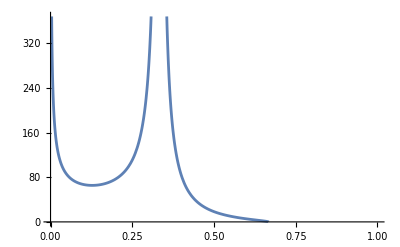

```mathematica
Plot[Subscript[M, total][x,x],{x,0,1}]
```

Hence, the two expressions are equivalent. The total orbital energy of the system in terms of the mass ratios is

```mathematica
1/2×M^2/a(Subscript[β, 1](Subscript[β, 2]^2+Subscript[β, 2] Subscript[β, 3]+Subscript[β, 3]^2)+Subscript[β, 2](Subscript[β, 1]^2+Subscript[β, 1] Subscript[β, 3]+Subscript[β, 3]^2)+Subscript[β, 3](Subscript[β, 1]^2+Subscript[β, 1] Subscript[β, 2]+Subscript[β, 2]^2))-(M^2(Subscript[β, 1] Subscript[β, 2]+Subscript[β, 2] Subscript[β, 3]+Subscript[β, 1] Subscript[β, 3]))/a/.a->M^(1/3)/ω^(2/3)//Simplify//Factor
```

1/2 M^(5/3) ω^(2/3) (-2+β_1+β_2+β_3) (β_1 β_2+β_1 β_3+β_2 β_3)

```mathematica
1/2×M^2/a(Subscript[ν, 1](Subscript[ν, 2]^2+Subscript[ν, 2] Subscript[ν, 3]+Subscript[ν, 3]^2)+Subscript[ν, 2](Subscript[ν, 1]^2+Subscript[ν, 1] Subscript[ν, 3]+Subscript[ν, 3]^2)+Subscript[ν, 3](Subscript[ν, 1]^2+Subscript[ν, 1] Subscript[ν, 2]+Subscript[ν, 2]^2))-(M^2(Subscript[ν, 1] Subscript[ν, 2]+Subscript[ν, 2] Subscript[ν, 3]+Subscript[ν, 1] Subscript[ν, 3]))/a//Simplify//Factor
```

(M^2 (-2+ν_1+ν_2+ν_3) (ν_1 ν_2+ν_1 ν_3+ν_2 ν_3))/(2 a)

Note that . In the limit where , we obtain the expression for the total orbital energy of a binary system.

```mathematica
%/.Subscript[ν, 3]->0
```

(M^2 ν_1 ν_2 (-2+ν_1+ν_2))/(2 a)

## Waveform of Elliptical Systems

```mathematica
Subscript[M, elliptic,11]=D[(D[(μ Subscript[a, 1]^2(1-e^2)^2 Cos[ψ[t]]^2/(1+e Cos[ψ[t]])^2), t]/.ψ'[t]->√(M/Subscript[a, 1]^3)(1-e^2)^(-3/2)(1+e Cos[ψ[t]])^2//FullSimplify), t]/.ψ'[t]->√(M/Subscript[a, 1]^3)(1-e^2)^(-3/2)(1+e Cos[ψ[t]])^2//Simplify
Subscript[M, elliptic,12]=D[(D[(μ Subscript[a, 1]^2(1-e^2)^2 Sin[2ψ[t]]/(2(1+e Cos[ψ[t]])^2)), t]/.ψ'[t]->√(M/Subscript[a, 1]^3)(1-e^2)^(-3/2)(1+e Cos[ψ[t]])^2//FullSimplify), t]/.ψ'[t]->√(M/Subscript[a, 1]^3)(1-e^2)^(-3/2)(1+e Cos[ψ[t]])^2//Simplify
Subscript[M, elliptic,22]=D[(D[(μ Subscript[a, 1]^2(1-e^2)^2 Sin[ψ[t]]^2/(1+e Cos[ψ[t]])^2), t]/.ψ'[t]->√(M/Subscript[a, 1]^3)(1-e^2)^(-3/2)(1+e Cos[ψ[t]])^2//FullSimplify), t]/.ψ'[t]->√(M/Subscript[a, 1]^3)(1-e^2)^(-3/2)(1+e Cos[ψ[t]])^2//Simplify
```

(M μ (3 e Cos[ψ[t]]+4 Cos[2 ψ[t]]+e Cos[3 ψ[t]]))/(2 (-1+e^2) a_1)

(M μ (4 Cos[ψ[t]]+e (3+Cos[2 ψ[t]])) Sin[ψ[t]])/((-1+e^2) a_1)

-(M μ (7 e Cos[ψ[t]]+4 Cos[2 ψ[t]]+e (4 e+Cos[3 ψ[t]])))/(2 (-1+e^2) a_1)

The plus polarization is

```mathematica
(Cos[ϕ]^2-Cos[ι]^2 Sin[ϕ]^2) Subscript[M, elliptic,11]-1/2 (3+Cos[2 ι]) Sin[2 ϕ] Subscript[M, elliptic,12]+(-Cos[ι]^2 Cos[ϕ]^2+Sin[ϕ]^2) Subscript[M, elliptic,22]//FullSimplify
```

(M μ (1/2 (3+Cos[2 ι]) Cos[2 ϕ] (5 e Cos[ψ[t]]+4 Cos[2 ψ[t]]+e (2 e+Cos[3 ψ[t]]))-2 e (e+Cos[ψ[t]]) Sin[ι]^2-(3+Cos[2 ι]) (4 Cos[ψ[t]]+e (3+Cos[2 ψ[t]])) Sin[2 ϕ] Sin[ψ[t]]))/(2 (-1+e^2) a_1)

```mathematica
1/(2 (-1+e^2) Subscript[a, 1])M μ (1/2 (3+Cos[2 ι])TrigReduce[Cos[2 ϕ] (5 e Cos[ψ[t]]+4 Cos[2 ψ[t]]+e (2 e+Cos[3 ψ[t]]))]-2 e (e+Cos[ψ[t]]) Sin[ι]^2-(3+Cos[2 ι]) TrigReduce[(4 Cos[ψ[t]]+e (3+Cos[2 ψ[t]])) Sin[2 ϕ] Sin[ψ[t]]])//FullSimplify
```

(M μ ((3+Cos[2 ι]) (4 Cos[2 (ϕ+ψ[t])]+e (2 e Cos[2 ϕ]+5 Cos[2 ϕ+ψ[t]]+Cos[2 ϕ+3 ψ[t]]))-4 e (e+Cos[ψ[t]]) Sin[ι]^2))/(4 (-1+e^2) a_1)

The cross polarization is

```mathematica
2 Cos[ι] (Cos[ϕ] Sin[ϕ] Subscript[M, elliptic,11]+Cos[ϕ]^2 Subscript[M, elliptic,12]-Sin[ϕ]^2 Subscript[M, elliptic,12]-Cos[ϕ] Sin[ϕ] Subscript[M, elliptic,22])//FullSimplify
```

(M μ Cos[ι] (4 Sin[2 (ϕ+ψ[t])]+e (2 e Sin[2 ϕ]+5 Sin[2 ϕ+ψ[t]]+Sin[2 ϕ+3 ψ[t]])))/((-1+e^2) a_1)